```mathematica
Quit[]
```

```mathematica
rawdata =Import["/Users/stevenschowalter/Desktop/phys191mms/HeData/mms_He_All.txt","Table"];
```

```mathematica
{totalnum} = Dimensions[rawdata];
```

```mathematica
Clear[k]
```

```mathematica
ProgressIndicator[Dynamic[k],{1,totalnum}]
```

```mathematica
k=1;
z=0;
While[(k+z)<totalnum,If[Dimensions[Dimensions[Take[rawdata,k]]]=={2},k++,{rawdata=Drop[rawdata,{k}],z++}]]
```

```mathematica
Dimensions[rawdata]
```

{59540,3}

```mathematica
num=Dimensions[rawdata][[1]]
```

59540

```mathematica
time=Take[rawdata,All,{3}];
voltage=Take[rawdata,All,{2}];
pulse=Take[rawdata,All,{1}];
```

```mathematica
temp=Table[0,{i,num}];
```

```mathematica
Do[temp[[i]]=ⅇ^(.0578*Log[voltage[[i]]]^8+.4845*Log[voltage[[i]]]^7+1.593*Log[voltage[[i]]]^6+2.521*Log[voltage[[i]]]^5+1.813*Log[voltage[[i]]]^4+.2846*Log[voltage[[i]]]^3-.1635*Log[voltage[[i]]]^2-.3503Log[voltage[[i]]]+.6568),{i,1,num}];
```

```mathematica
timetemp=Table[0,{i,num}];
Do[timetemp[[i]]=Flatten[{i,temp[[i]]},2],{i,1,num}]
```

```mathematica
temp;
```

```mathematica
voltage;
```

```mathematica
num
```

59540

```mathematica
Mean[Take[timetemp,{6870,6920}]]
```

{6895,2.17745}

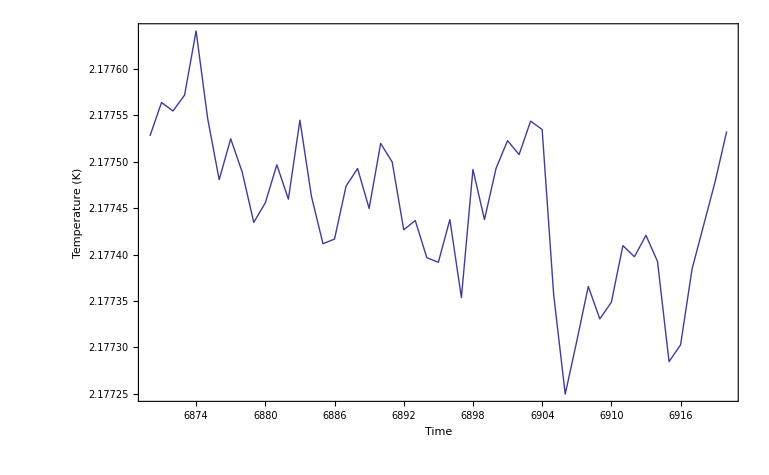

```mathematica
heating=ListPlot[Take[timetemp,{6870,6920}],PlotRange->All,Frame->True,Axes->False, Joined->True,FrameLabel->{"Time","Temperature (K)"}]
```

```mathematica
Export["heating.eps",heating]
```

heating.eps

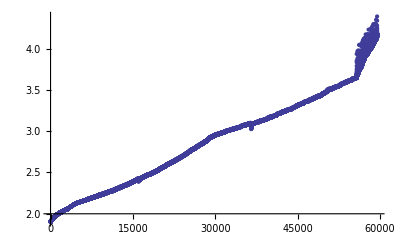

```mathematica
ListPlot[timetemp]
```

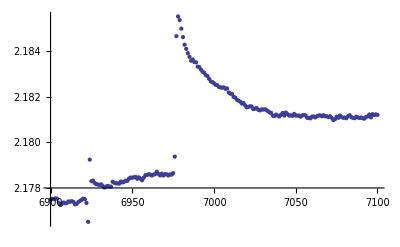

```mathematica
ListPlot[Take[timetemp,{6900,7100}]]
```

```mathematica
num
```

59540

```mathematica
Q=10.5^2/1116 10^-2
```

0.000987903

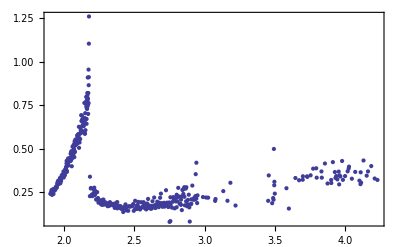

```mathematica
threshold=.001;
threshold2=.004;
threshold3=.0098;
threshold4=.0098;
dT={};
Do[If[temp[[i+2]][[1]]>temp[[i]][[1]]+threshold,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-5,i}]][[1]]+Mean[Take[temp,{i+3,i+7}]][[1]])}}]}],{i,6,6977-7}]


Do[If[temp[[i+1]][[1]]>temp[[i]][[1]]+threshold2,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-10,i}]][[1]]+Mean[Take[temp,{i+50,i+80}]][[1]])}}]}],{i,6977,16023}]
Do[If[temp[[i+1]][[1]]>temp[[i]][[1]]+threshold2,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-10,i}]][[1]]+Mean[Take[temp,{i+50,i+60}]][[1]])}}]}],{i,16025,30000}]

Do[If[temp[[i+1]][[1]]>temp[[i]][[1]]+threshold3,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-20,i-10}]][[1]]+Mean[Take[temp,{i+15,i+50}]][[1]])}}]}],{i,30001,54500}]

Do[If[temp[[i+1]][[1]]>temp[[i]][[1]]+threshold4,{dT=Join[dT,{{temp[[i]][[1]],Q*10/(-Mean[Take[temp,{i-10,i-3}]][[1]]+Mean[Take[temp,{i+30,i+50}]][[1]])}}]}],{i,55000,num-100}]

ListPlot[dT,PlotRange->All,Frame->True]
```

```mathematica
dV=Take[dT,All,{2}];
V=Take[dT,All,{1}];
```

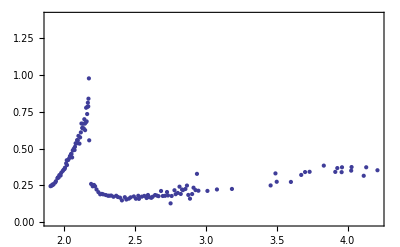

```mathematica
avgsize=3;
avgnum=Quotient[410,avgsize];
avgV=Take[V,{1,-1,avgsize}];
avgdV=Table[0,{i,avgnum}];
Do[avgdV[[i]]=Mean[Take[dV,{1+avgsize(i-1),avgsize(i)}]],{i,1,avgnum}]
avgdT=Table[0,{i,avgnum}];
Do[avgdT[[i]]=Flatten[{avgV[[i]],avgdV[[i]]},2],{i,1,avgnum}]
ListPlot[avgdT,PlotRange->{0,1.4},Joined->False,Frame->True]
```

```mathematica
avgdT;
```

```mathematica
avgnum
```

136

```mathematica
Dimensions[dT]
```

{410,2}

```mathematica
{539,2}
```

{539,2}

```mathematica
Dimensions[avgdT]
```

{136,2}

```mathematica
normavgdT=Table[0,{i,136}];
```

```mathematica
Do[normavgdT[[i]]={Take[avgdT[[i]],{1}][[1]],Take[avgdT[[i]],{2}][[1]]-(0.015932467940417003*Take[avgdT[[i]],{1}][[1]]+0.0012545580454563976*(Take[avgdT[[i]],{1}][[1]])^3)},{i,1,136}]
```

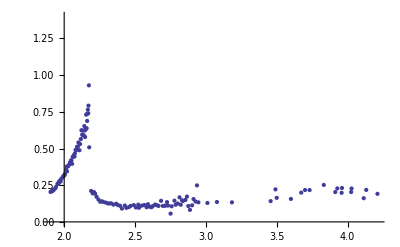

```mathematica
ListPlot[normavgdT,PlotRange->{0,1.4}]
```

```mathematica
finalC=Table[1,{i,136}];
Do[finalC[[i]]={normavgdT[[i]][[1]],(1/25.4)/(.0005385)normavgdT[[i]][[2]]},{i,1,136}]
```

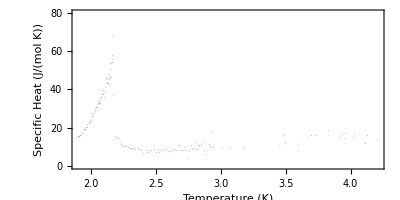

```mathematica
plot=ListPlot[finalC,PlotRange->{0,80},Frame->True,Joined->False,AspectRatio->1/2,FrameLabel->{"Temperature (K)","Specific Heat (J/(mol K))"},PlotStyle->{PointSize[.0001]}]
```

```mathematica
Export["lambdapt.eps",plot]
```

lambdapt.eps

$Aborted